```mathematica
b[k_, K1_, K2_, U1_, U2_]:= (-1+Sqrt[1+4((K1 k U1)/2+ K2 k U1 U2)^2])/(2((K1 k U1)/2+ K2 k U1 U2));
```

```mathematica
P[k_] := 1/41;
```

```mathematica
meank = Sum[k P[k], {k, 30, 70}]
```

50

```mathematica
f1[K1_, K2_, U1_, U2_]:= 1/meank Sum[P[k] k b[k, K1, K2, U1, U2], {k, 30, 70}];
```

```mathematica
f2[K1_, K2_, U1_, U2_]:= 1/meank Sum[P[k] k b[k, K1, K2, U1, U2]^2, {k, 30, 70}];
```

```mathematica
root[K1_,K2_] := FindRoot[{U1-f1[K1,K2, U1, U2]== 0, U2-f2[K1,K2, U1, U2]== 0}, {{U1, 0.5}, {U2, 0.5}}]
```

```mathematica
root1[K1_, K2_] := root[K1, K2][[1]][[2]]
```

```mathematica
root[0.03,0.05]
```

{U1→0.721404,U2→0.523423}

```mathematica
root[0.4,0.1]
```

{U1→0.94874,U2→0.900289}

```mathematica
root1[0.4,0.1]
```

0.94874

```mathematica
root2[K1_, K2_]:= root[K1, K2][[2]][[2]]
```

```mathematica
root2[0.4,0.1]
```

0.900289

```mathematica
plot1 = Table[{K1, root1[K1,0.1]}, {K1, 0.4, -0.2, -0.02}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{0.4,0.94874},{0.38,0.946723},{0.36,0.944533},{0.34,0.942142},{0.32,0.939522},{0.3,0.936634},{0.28,0.933432},{0.26,0.929858},{0.24,0.925837},{0.22,0.921271},{0.2,0.916026},{0.18,0.90992},{0.16,0.902687},{0.14,0.893925},{0.12,0.882977},{0.1,0.868669},{0.08,0.848528},{0.06,0.815533},{0.04,0.684385},{0.02,0.723025},{0.,0.763191},{-0.02,0.812761},{-0.04,0.878246},{-0.06,0.959522},{-0.08,1.07515},{-0.1,1.27179},{-0.12,-3.66262×10^-13},{-0.14,-5.16276×10^-10},{-0.16,-2.31251×10^-11},{-0.18,-3.05588×10^-11},{-0.2,-2.92737×10^-10}}

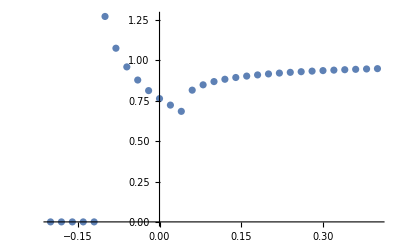

```mathematica
ListPlot[plot1, PlotRange->All]
```